# Gaussian bundles optics

Arthur Smirnov, Alexander Shabanov, Alexander Nekhaev, Ilnaz Mingaraev

Importing dataset

```mathematica
SetDirectory[NotebookDirectory[]];
data =Import["lab33.xlsx"];
```

```mathematica
settings=data[[4]];
data1=data[[1]][[2;;All,All]];
data2=data[[2]][[2;;All,All]];
data3 =data[[3]][[2;;All,All]];
TableForm[settings]
TableForm[Transpose[data[[1]]]]
TableForm[Transpose[data[[2]]]]
TableForm[Transpose[data[[3]]]]
```

| От линзы до приемника, см | От лазера до линзы, см
Part 1 |  | 
Part 2 | 8. | 43.5
Part 3 | 15. | 36.5

Coordinate | 0. | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9
Voltage | 0. | 1. | 2. | 7. | 20. | 56. | 143. | 439. | 471. | 352. | 204. | 96. | 43. | 17. | 6. | 2. | 1. | 1. | 0.

Coordinate | 0. | 0.025 | 0.05 | 0.075 | 0.1 | 0.125 | 0.15 | 0.175 | 0.2 | 0.225 | 0.25 | 0.275 | 0.3 | 0.325 | 0.35 | 0.375 | 0.4 | 0.425 | 0.45 | 0.475 | 0.5 | 0.525 | 0.55 | 0.575 | 0.6 | 0.625 | 0.65 | 0.675 | 0.7 | 0.725 | 0.75 | 0.775 | 0.8 | 0.825 | 0.85 | 0.875 | 0.9 | 0.925 | 0.95 | 0.975
Voltage | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 2. | 2. | 2. | 2. | 2. | 2. | 3. | 3. | 6. | 14. | 41. | 99. | 201. | 356. | 515. | 621. | 633. | 474. | 334. | 194. | 76. | 22. | 6. | 3. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2.

Coordinate | 0. | 0.025 | 0.05 | 0.075 | 0.1 | 0.125 | 0.15 | 0.175 | 0.2 | 0.225 | 0.25 | 0.275 | 0.3 | 0.325 | 0.35 | 0.375 | 0.4 | 0.425 | 0.45 | 0.475 | 0.5 | 0.525 | 0.55 | 0.575 | 0.6 | 0.625 | 0.65 | 0.675 | 0.7 | 0.725 | 0.75 | 0.775 | 0.8 | 0.825 | 0.85 | 0.875 | 0.9 | 0.925 | 0.95 | 0.975 | 1. | 1.025 | 1.05 | 1.075 | 1.1 | 1.125 | 1.15 | 1.175 | 1.2 | 1.225 | 1.25 | 1.275 | 1.3 | 1.325 | 1.35 | 1.375 | 1.4 | 1.425 | 1.45 | 1.475 | 1.5 | 1.525 | 1.55 | 1.575 | 1.6 | 1.625 | 1.65 | 1.675 | 1.7 | 1.725 | 1.75 | 1.775 | 1.8 | 1.825 | 1.85 | 1.875 | 1.9 | 1.925 | 1.95
Voltage | 0. | 1. | 1. | 1. | 2. | 2. | 3. | 4. | 5. | 6. | 7. | 9. | 10. | 12. | 14. | 16. | 18. | 20. | 24. | 26. | 29. | 32. | 34. | 37. | 40. | 42. | 44. | 46. | 49. | 51. | 53. | 54. | 56. | 59. | 60. | 62. | 63. | 64. | 64. | 64. | 64. | 63. | 61. | 60. | 58. | 56. | 54. | 52. | 49. | 46. | 43. | 40. | 37. | 33. | 30. | 26. | 23. | 21. | 18. | 16. | 14. | 13. | 11. | 10. | 8. | 7. | 6. | 5. | 4. | 3. | 2. | 2. | 1. | 1. | 1. | 1. | 1. | 1. | 0.

Introducing Gaussian function

```mathematica
Gauss[x_]:=A Evaluate[PDF[NormalDistribution[x0,σ],x]];
```

Fitting

```mathematica
fit1=FindFit[data1,Gauss[x],{A,x0,σ},x];
fit2=FindFit[data2,Gauss[x],{A,x0,σ},x];
fit3=FindFit[data3,Gauss[x],{A,x0,σ},x];
```

Fit results

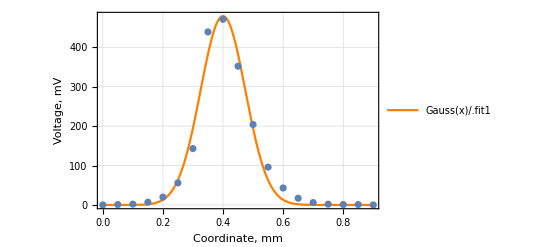

```mathematica
Show[
Plot[
Gauss[x]/.fit1,{x,0,Max[data1[[All,1]]]},
PlotStyle->Orange,
FrameLabel->{"Coordinate, mm", "Voltage, mV","Part 1"},
PlotTheme->"Detailed"
],
ListPlot[data1]
]
```

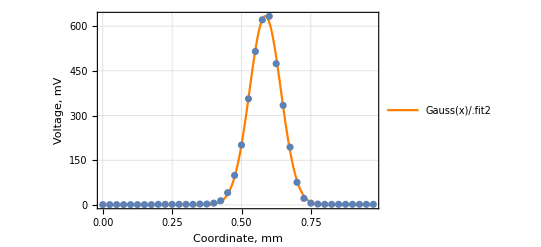

```mathematica
Show[
Plot[
Gauss[x]/.fit2,{x,0,Max[data2[[All,1]]]},
PlotStyle->Orange,
FrameLabel->{"Coordinate, mm", "Voltage, mV", "Part 2"},
PlotTheme->"Detailed"
],
ListPlot[data2]
]
```

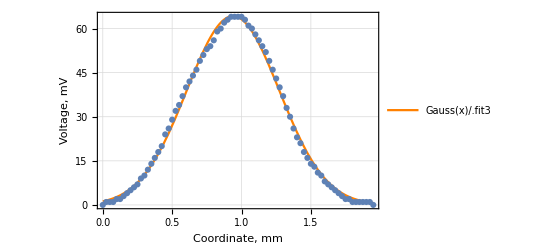

```mathematica
Show[
Plot[
Gauss[x]/.fit3,{x,0,Max[data3[[All,1]]]},
PlotStyle->Orange,
FrameLabel->{"Coordinate, mm", "Voltage, mV", "Part 3"},
PlotTheme->"Detailed"
],
ListPlot[data3]
]
```

Half-widths

```mathematica
w[c_]:=2 √(2Log[2])c;
w1=w[σ/.fit1];
w2=w[σ/.fit2];
w3=w[σ/.fit3];
Print["w_1=",w1]
Print["w_2=",w2]
Print["w_3=",w3]
```

w_1=0.17549

w_2=0.133194

w_3=0.785122

## Searching focal distances

Theory :

q_2=(Aq_1+B)/(Cq_1+D)

(A | B
C | D)=(1-l_2/f | l_1+l_2-(l_1 l_2)/f
-1/f | 1-l_1/f)

Calculating F from equation:

π/(Im(1/q_2)*λ)=w_2^2

(F inside q_2)

```mathematica
solutions=Solve[ω^2==ω0^2(1+((λ z)/(π ω0^2))^2),ω0];
ω01=Re[ω0/.(solutions/.{λ->680*10^-9,z->0.515,ω-> w1*10^-3})[[2]]];
Q2[m_,q_]:=(m[[1,1]]*q+m[[1,2]])/(m[[2,1]]*q+m[[2,2]]);
m[l1_,l2_]=({{1-l2/f, l1+l2-(l1 l2)/f}, {-1/f, 1-l1/f}});
mp=m[
settings[[3,2;;3]][[1]]*10^-2,
settings[[3,2;;3]][[2]]*10^-2
];
q2=Q2[mp,(π ω01^2)/(680*10^-9)I];
f1=Re[f/.Solve[π/(Im[1/q2]680*10^-9)==(w2*10^-3)^2,f]][[1]];
Print["f_1=",f1, " meters"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

f_1=0.157453 meters

```mathematica
mp2=m[
settings[[4,2;;3]][[1]]*10^-2,
settings[[4,2;;3]][[2]]*10^-2
];
q22=Q2[mp2,(π ω01^2)/(680*10^-9)I];
f2=Re[f/.Solve[Reduce[π/(Im[1/q22]680*10^-9)==(w3*10^-3)^2,f][[1]],f][[1]]];
Print["f_2=",f2," meters"]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

f_2=0.169592 meters

## Hauling point

```mathematica
q3=Q2[({{1, z}, {0, 1}}),q2/.f->f1];
z1=(Re[z]/.Solve[Reduce[Re[q3]==0,z],Re[z]])[[1]];
Print["z_1=",z1," meters"]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

z_1=-0.298444 meters

```mathematica
q4=Q2[({{1, z}, {0, 1}}),q22/.f->f2];
z2=(Re[z]/.Solve[Reduce[Re[q4]==0,z],Re[z]])[[1]];
Print["z_2=",z2," meters"]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

z_2=-0.20194 meters

## Hauling width

```mathematica
ωz1=√(Im[q2/.f->f1]*λ/π)/.λ->680*10^-9;
Print["ω_z_1=",ωz1*10^3, " mm"]
```

ω_z_1=0.130823 mm

```mathematica
ωz2=√(Im[q22/.f->f2]*λ/π)/.λ->680*10^-9;
Print["ω_z_2=",ωz2*10^3, " mm"]
```

ω_z_2=0.145422 mm

## Questions

Какие элементы оптики пригодны для расчетов ГОС, почему другие не применимы.

Резонатор с линзой.

Устойчивый резонатор.Добротность резонатора.

На выходе из лазера стоит линза мелкая, с подкручиваемым фокусом.Попробуйте из полученных вами данных найти её фокусное расстояние.